/home/gwang/Code/AktMuscleCode/OB_Normal_Gsu10_iVol0p075/

{5.508,5.508,5.508,5.508,5.508,5.50801,5.50801,5.50802,5.50802,5.50803,5.50803,5.50804,5.50805,5.50806,5.50807,5.50808,5.50809,5.5081,5.50812,5.50813,5.50815,5.50816,5.50818,5.50819,5.50821,5.50823,5.50825,5.50827,5.50829,5.50831,5.50833,5.50836,5.50838,5.5084,5.50843,5.50846,5.50848,5.50851,5.50854,29923,5.36115,5.36119,5.36123,5.36126,5.3613,5.36133,5.36137,5.3614,5.36144,5.36147,5.36151,5.36154,5.36158,5.36162,5.36165,5.36169,5.36172,5.36176,5.36179,5.36183,5.36186,5.3619,5.36193,5.36197,5.36201,5.36204,5.36208,5.36211,5.36215,5.36218,5.36222,5.36225,5.36229,5.36232,5.36236,5.36239,5.36243,5.36246,5.3625}
 |  |  |  |

0.0261607

3.83492

1.46855

0.

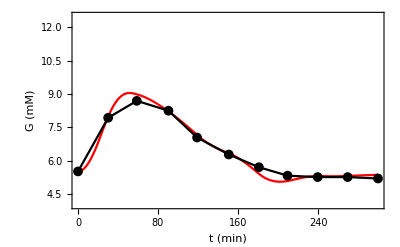

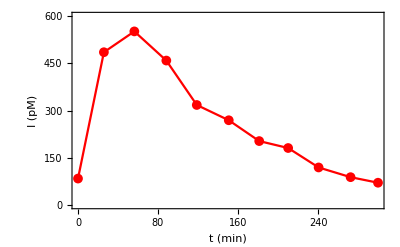

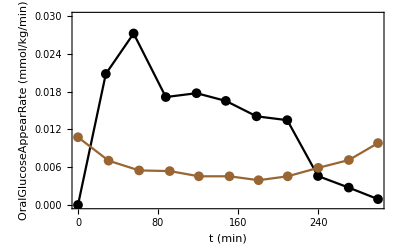

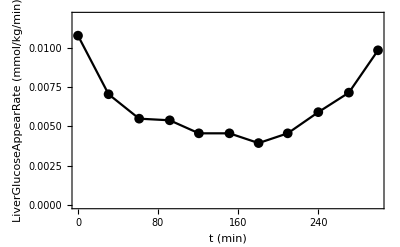

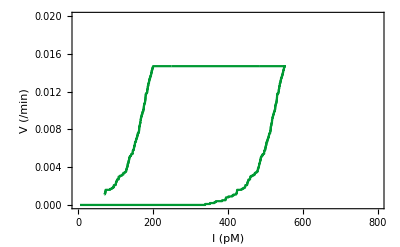

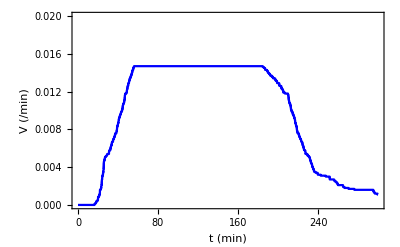

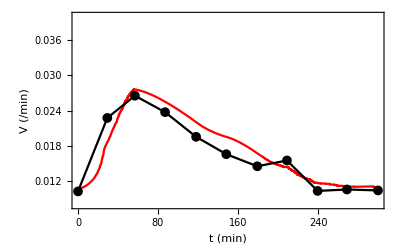

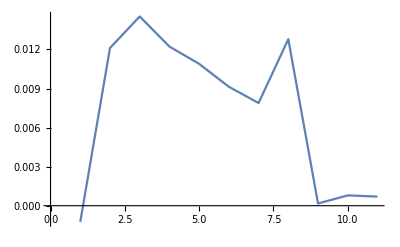

```mathematica
Remove["Global`*"];

NotebookDirectory[]

h=0.01;

OralData=Flatten[Import[ToFileName[NotebookDirectory[],"iOral.txt"],"Data"]];
LiverData=Flatten[Import[ToFileName[NotebookDirectory[],"iLiver.txt"],"Data"]];
OraliverData=Flatten[Import[ToFileName[NotebookDirectory[],"iMeal.txt"],"Data"]];
s0=OraliverData[[1]];

BestParaBlock=Flatten[Import[ToFileName[NotebookDirectory[],"BestParaBlock.txt"],"Data"]];
Vsu=BestParaBlock[[4]];
Gsu=BestParaBlock[[5]];
Ome=BestParaBlock[[6]];


G=Flatten[Import[ToFileName[NotebookDirectory[],"G.txt"],"Data"]]
Len = Length[G];
Insulin=Flatten[Import[ToFileName[NotebookDirectory[],"I.txt"],"Data"]];

V=Flatten[Import[ToFileName[NotebookDirectory[],"V.txt"],"Data"]];


VofI = MapThread[List,{Insulin,V}];

V0=s0/Ome/G[[1]]

GGsu = G-Gsu;
GGsu = GGsu /. _?Negative -> 0;

VGO= (V+V0) G Ome + Vsu GGsu Ome;

VG = V G;

TotalV0 = (Total[G]-0.5 G[[1]]-0.5 G[[Len]]) V0 Ome h

TotalVI=(Total[VG]-0.5 VG[[1]]-0.5 VG[[Len]])  Ome h

TotalVsu=Total[GGsu] Vsu Ome h

VGOData=Flatten[Import[ToFileName[NotebookDirectory[],"VGOData.txt"],"Data"]];
VGOTime=Flatten[Import[ToFileName[NotebookDirectory[],"VGOTime.txt"],"Data"]];
VGODataTime = MapThread[List,{VGOTime,VGOData}];




GData=Flatten[Import[ToFileName[NotebookDirectory[],"GData.txt"],"Data"]];
IData=Flatten[Import[ToFileName[NotebookDirectory[],"IData.txt"],"Data"]];
GTime=Flatten[Import[ToFileName[NotebookDirectory[],"GTime.txt"],"Data"]];
ITime=Flatten[Import[ToFileName[NotebookDirectory[],"ITime.txt"],"Data"]];
OralTime=Flatten[Import[ToFileName[NotebookDirectory[],"iOralTime.txt"],"Data"]];
LiverTime=Flatten[Import[ToFileName[NotebookDirectory[],"iLiverTime.txt"],"Data"]];
LenTime=Length[GTime];
GDataTime = MapThread[List,{GTime,GData}];
IDataTime = MapThread[List,{ITime,IData}];
OralDataTime=MapThread[List,{OralTime,OralData}];
LiverDataTime=MapThread[List,{LiverTime,LiverData}];




Show[
ListLinePlot[G,DataRange->{0,Len*h},PlotRange->{{0,300},{4,12.5}},Frame->True,FrameLabel->{"t (min)","G (mM)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListLinePlot[GDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Black]
]

Export[ToFileName[NotebookDirectory[],"GData.eps"],%];

(*
Show[
ListLinePlot[Insulin,DataRange->{0,Len*h},PlotRange->{{0,300},{0,600}},Frame->True,FrameLabel->{"t (min)","I (pM)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListPlot[IDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Red]
]
*)

ListLinePlot[IDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Red,PlotRange->{{0,300},{0,600}},Frame->True,FrameLabel->{"t (min)","I (pM)"},LabelStyle->20,FrameTicksStyle->Directive[18]]

Export[ToFileName[NotebookDirectory[],"IData.eps"],%];

Show[
ListLinePlot[OralDataTime,PlotMarkers->{Automatic,10},PlotStyle->Black,PlotRange->{{0,300},{0,0.030}},Frame->True,FrameLabel->{"t (min)","OralGlucoseAppearRate (mmol/kg/min)"},LabelStyle->15,FrameTicksStyle->Directive[14]],
ListLinePlot[LiverDataTime,PlotMarkers->{Automatic,10},PlotStyle->Brown]
]
Export[ToFileName[NotebookDirectory[],"Oral.eps"],%];


ListLinePlot[LiverDataTime,PlotMarkers->{Automatic,10},PlotStyle->Black,PlotRange->{{0,300},{0,0.012}},Frame->True,FrameLabel->{"t (min)","LiverGlucoseAppearRate (mmol/kg/min)"},LabelStyle->15,FrameTicksStyle->Directive[18]]

Export[ToFileName[NotebookDirectory[],"Liver.eps"],%];

ListLinePlot[VofI,PlotRange->{{0,800},{0,0.02}},Frame->True,FrameLabel->{"I (pM)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->RGBColor[0,0.6,0.2]]


Export[ToFileName[NotebookDirectory[],"VI.eps"],%];

ListLinePlot[V,DataRange->{0,Len*h},PlotRange->{{0,300},{0,0.02}},Frame->True,FrameLabel->{"t (min)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Blue]

Show[
ListLinePlot[VGO,DataRange->{0,Len*h},PlotRange->{{0,300},{0.008,0.04}},Frame->True,FrameLabel->{"t (min)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListLinePlot[VGODataTime,PlotMarkers->{Automatic, 10},PlotStyle->Black]
]

Export[ToFileName[NotebookDirectory[],"VGO.eps"],%];

ListLinePlot[VGOData/GData/0.075-ConstantArray[V0,Length[VGOData]]]
```